Diagonalization of the modified Rabi model with three-level atoms and 2-mode cavity
The example below shows a Λ-type atom coupled to 2 photons with different frequencies, ω1 and ω2
The coupling strengths to the two photon modes are λ1 and λ2 respectively.
Can modify to study other configurations for the atom and the photon-atom coupling

Module 1: Basic setting
Basis arrangement: (|e,0,0> |f,0,0> |g,0,0> |e,0,1> |f,0,1> |g,0,1> ... )
Value of α: e-->2, f-->1, g-->0 (e--highest state, f-middle state, g-ground state)

```mathematica
Clear["Global`*"]; (* Clear global kernel *)

nphoton=10; (* Max photon number *)
dim=3*(nphoton+1)^2; (* Dimension of Hilbert space *)
max=20; (* No of eigenvalues wanted *)
Print["Dimension of Hilbert space: ",dim]

pos[α_,n1_,n2_]:=3n1*(nphoton+1)+3(n2+1)-α;

ωe=1;
ωf=0.1;
ωg=0;

σa={{ωe,0,0},{0,ωf,0},{0,0,ωg}}; (* Pauli matrix for atom *)
σge={{0,0,1},{0,0,0},{1,0,0}}; (* Pauli x for ge *)
σfe={{0,1,0},{1,0,0},{0,0,0}}; (* Pauli x for fe *)

σpge={{0,0,1},{0,0,0},{0,0,0}}; (* Raising for ge *)
σmge={{0,0,0},{0,0,0},{1,0,0}}; (* Lowering for ge *)
σpfe={{0,1,0},{0,0,0},{0,0,0}}; (* Raising for fe *)
σmfe={{0,0,0},{1,0,0},{0,0,0}}; (* Lowering for fe *)

idenphoton=IdentityMatrix[nphoton+1];
idenatom=IdentityMatrix[3];

(* Annihilation for photon *)
a=Table[0.,nphoton+1,nphoton+1]; 
Do[a[[i,i+1]]=N[Sqrt[i]];,{i,1,nphoton}];

(* Creation for photon *)
adag=Transpose[a];

(* Rabi Hamiltonian *)
H[ω1_,ω2_,λ1_,λ2_]:=KroneckerProduct[idenphoton,idenphoton,σa]+ω1*KroneckerProduct[adag.a,idenphoton,idenatom]+ω2*KroneckerProduct[idenphoton,adag.a,idenatom]+λ1*KroneckerProduct[a+adag,idenphoton,σge]+λ2*KroneckerProduct[idenphoton,a+adag,σfe];

(* Jaynes-Cummings Hamiltonian *)
HRWA[ω1_,ω2_,λ1_,λ2_]:=KroneckerProduct[idenphoton,idenphoton,σa]+ω1*KroneckerProduct[adag.a,idenphoton,idenatom]+ω2*KroneckerProduct[idenphoton,adag.a,idenatom]+λ1*KroneckerProduct[a+adag,idenphoton,σge]+λ2*KroneckerProduct[idenphoton,a+adag,σfe];
```

Dimension of Hilbert space: 363

Module 2 : Numerical diagonalization
Here, the example studies the spectrum as a function of λ2 (coupling between |e> and |f>)
Motivation: Will add external drive and study how dark states are modified with cavity photons

```mathematica
Timing[
ω1=ωe-ωg;
ω2=ωe-ωf;
λ1=0.05; (* λ1 describes photons that couple |g> and |e> *)

Clear[enRabilist, enJClist];

Do[enRabilist[i]={};,{i,1,max}];
Do[enJClist[i]={};,{i,1,max}];

(* 
Do[vecRabilist[i]={};,{i,1,max}]; 
Do[vecJClist[i]={};,{i,1,max}]; 
*)

Do[
Do[
(* Change the function to "Eigensystem" if eigenvectors are also needed *)
solRabi=Eigenvalues[H[ω1,ω2,λ1,λ2]+100*IdentityMatrix[dim],-max];
solJC=Eigenvalues[HRWA[ω1,ω2,λ1,λ2]+100*IdentityMatrix[dim],-max];
enRabilist[i]=Append[enRabilist[i],{λ2,solRabi[[max+1-i]]-100}];
enJClist[i]=Append[enJClist[i],{λ2,solJC[[max+1-i]]-100}];
,{i,1,max}];
,{λ2,0,0.1,0.002}]

]
```

{67.4912,Null}

Module 3: Plot the numerical results (expect to see bands)

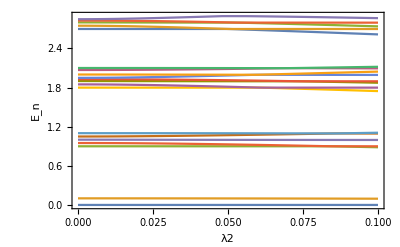

-Graphics-

```mathematica
lowest=1;
highest=max;

plotRabi={};
plotJC={};
Do[
plotRabi=Append[plotRabi,enRabilist[i]];
plotJC=Append[plotJC,enJClist[i]];
,{i,lowest,highest}];

ListPlot[plotRabi,Joined->True,Frame->True,FrameLabel->{"λ2","E_n"}]
ListPlot[plotJC,Joined->True,Frame->True,FrameLabel->{"λ2","E_n"}]
```